# Relax results

Changes in position during relaxation, as a function of relaxation time. Used for “Changes in filament microstructures during direct ink writing with yield stress fluid support”
Last updated by Leanne Friedrich, November 2019

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
<<"Mathematica\\relaxresults.wl";
bigtable2 = Import["Tables\\bigtable2_middleedge.csv"];
changetable = Import["Tables\\changetable_middleedge.csv"];
```

## relax times

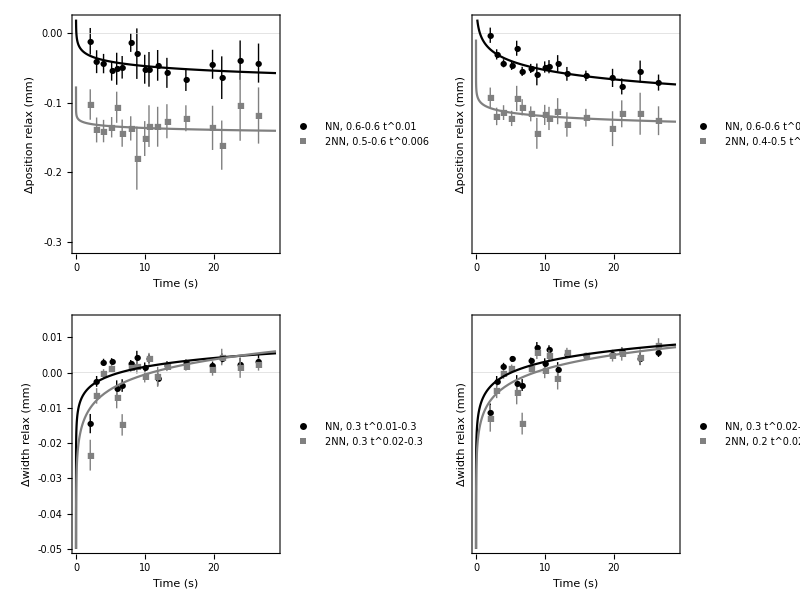

```mathematica
rpg2 = relaxplotgrid[changetable,PS, False, 3.25]
```

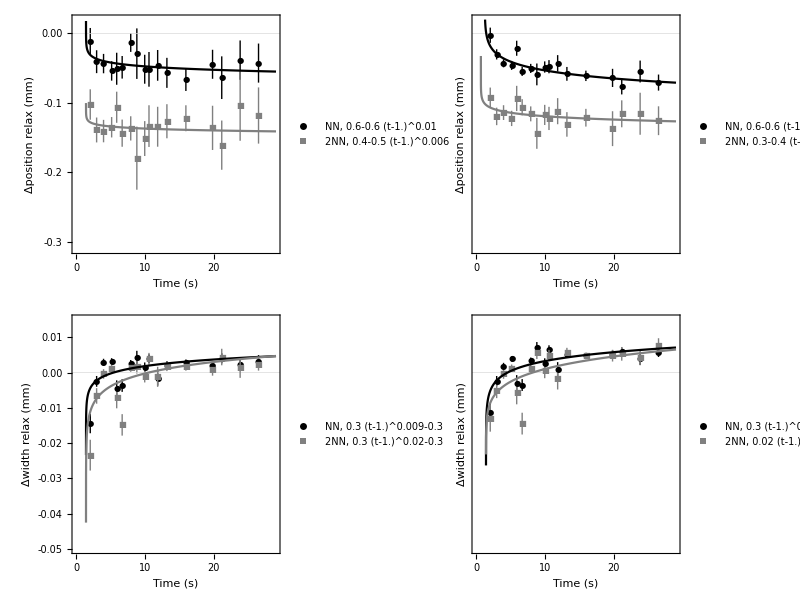

```mathematica
rpg1 = relaxplotgrid[changetable,PS, True, 5]
```

```mathematica
logrpg = logrelax[changetable]
```

-Graphics-

```mathematica
Export["figures\\relaxvtime.pdf", rpg2];
Export["figures\\relaxvtimed.pdf", rpg1];
```

```mathematica
Export["figures\\logrelaxvtime.pdf", logrpg];
```